# Basic NCR Calculations

```mathematica
Clear["Global`*"]
```

Ultimately, we only need to  keep track of changing concentrations of two variables, free activator (A) and cleaved fluorescent) reporter (S)
However, we must also somehow account for the binding and unbinding of Cas13:cRNA:Target to the reporter, as well as the caged activator. 
Thus we end up with two additional compound variables. In general, these must be included explicitly in the ODE system. In the limiting case where
Binding/unbinding is much slower than catalysis, we can use the Michaelis Menten approximation to get around having to track the compound 
variables explicitly

### Full Minimal System of ODEs to Capture Core Elements of NCR Reaction

#### Define System of ODEs

(1) Free activator (A). 
Note that C0 indicates initial concentration of caged activator, R0 is the target viral load, and S0 is initial concentration of dark (uncleaved) reporter

```mathematica
eqA = A'[t] == -((C0-A[t]) +(S0-F[t]))*(R0+A[t])*kon + (AC[t] + AS[t])*koff + AS[t]*kcat+2*AC[t]*kcat;
```

(2) Fluorescent Reporter

```mathematica
eqF = F'[t] == AS[t]*kcat
```

F'[t]==kcat AS[t]

(3) Activator-Reporter compound

```mathematica
eqAS = AS'[t] == -AS[t]*(kcat+koff) + (R0+A[t])*(S0-F[t])*kon
```

AS'[t]==-(kcat+koff) AS[t]+kon (R0+A[t]) (S0-F[t])

(4) Activator-Caged Activator compound

```mathematica
eqAC = AC'[t] == -AC[t]*(kcat+koff)+ (R0+A[t])*(C0-A[t])*kon
```

AC'[t]==kon (C0-A[t]) (R0+A[t])-(kcat+koff) AC[t]

#### Define Initial Conditions and Rate Constants

```mathematica
rateValVec = {kon->1,koff->2000,kcat->20};
```

```mathematica
constantParamVecNCR = {C0->50,R0->.01,S0->200};
```

```mathematica
constantParamVecSherlock = {C0->0,R0->.01,S0->200};
```

```mathematica
initialConditions = {A[0] == 0,F[0]==0,AS[0]==0,AC[0]==0};
```

#### Solve System

```mathematica
{eqANCR,eqFNCR,eqASNCR,eqACNCR} = {eqA,eqF,eqAS,eqAC}/.rateValVec/.constantParamVecNCR;
```

```mathematica
{eqASher,eqFSher,eqASSher,eqACSher} = {eqA,eqF,eqAS,eqAC}/.rateValVec/.constantParamVecSherlock;
```

```mathematica
NCRSol = NDSolve[{eqANCR,eqFNCR,eqACNCR,eqASNCR,initialConditions},{A,F,AS,AC},{t,0,100}];
```

```mathematica
SherSol = NDSolve[{eqASher,eqFSher,eqACSher,eqASSher,initialConditions},{A,F,AS,AC},{t,0,100}];
```

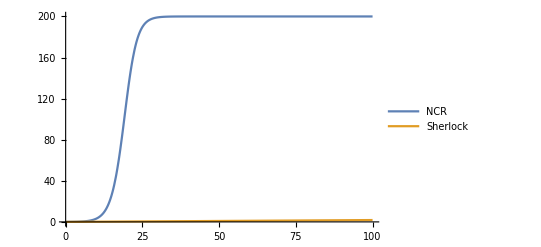

```mathematica
Plot[{Evaluate[F[t]/.NCRSol],Evaluate[F[t]/.SherSol]},{t,0,100},PlotRange->All,PlotLegends->{"NCR","Sherlock"}]
```

### Minimal System of ODEs with Michaelis-Menten Kinetics

#### Define System of ODEs

(0) Define Michaelis constant

```mathematica
Km = (kcat + koff)/kon;
```

(1) Free activator (A).

```mathematica
eqAmm = A'[t] == (R0+A[t])*(C0-A[t]) / (Km+ C0-A[t]) *kcat;
```

(2) Fluorescent Reporter

```mathematica
eqFmm = F'[t] == (R0+A[t])*(S0-F[t]) / (Km+ S0-F[t]) *kcat;
```

#### Solve System

```mathematica
{eqAmmNCR,eqFmmNCR} = {eqAmm,eqFmm}/.rateValVec/.constantParamVecNCR;
```

```mathematica
{eqAmmSher,eqFmmSher} = {eqAmm,eqFmm}/.rateValVec/.constantParamVecSherlock;
```

```mathematica
NCRmmSol = NDSolve[{eqAmmNCR,eqFmmNCR,initialConditions},{A,F},{t,0,1000}];
```

```mathematica
ShermmSol = NDSolve[{eqAmmSher,eqFmmSher,initialConditions},{A,F},{t,0,1000}];
```

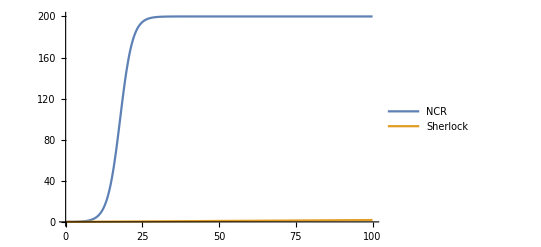

```mathematica
Plot[{Evaluate[F[t]/.NCRmmSol],Evaluate[F[t]/.ShermmSol]},{t,0,100},PlotRange->All,PlotLegends->{"NCR","Sherlock"}]
```

## Compare Full Solution to MM Approximation

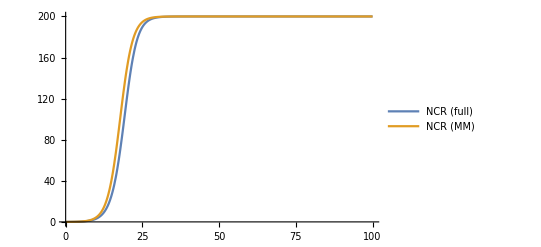

```mathematica
Plot[{Evaluate[F[t]/.NCRSol],Evaluate[F[t]/.NCRmmSol]},{t,0,100},PlotRange->All,PlotLegends->{"NCR (full)","NCR (MM)"}]
```

Looks like the MM approximation works well for the rates we have, which makes sense--the catalytic rate (kcat) is the slowest rate by an order of magnitude